Quantitative Fundraising Appeal Prioritization System

written by Sean Madsen, IT manager for Bikes Not Bombs, 2013

# Introduction

## About this document

This document was made with Mathematica by Sean Madsen in 2013. You may be reading it in PDF form, which will help you get an understanding of the underlying algorithms used in the QFAP system. However, reading the .nb document with the Mathematica application will allow you interact and change it. The application is proprietary, so if you do not have it, you won’t be able to modify the source document. But you do have the option of installing the free “Mathematica Reader” application to view the .nb file and interact with some of the graphs (but not make changes). If you will be reading this document in depth I highly recommend reading it using either Mathematica Reader, or Mathematica.

## Intended Audience

The content herein serves to document the highly sophisticated process of culling contacts for fundraising appeals, as developed by Sean Madsen beginning in 2013. It is technical in nature and primarily designed for the computationally competent. However, concepts are first explained qualitatively so as to remain digestible for less mathematically inclined readers, should the need arise. It is not (yet?) designed for distribution outside of Bikes Not Bombs.

## General overview of the process

Bundling

First, all contacts are “bundled”. Connections are made between contacts based on: (1) certain types of relationships (“household member”, for example), and (2) presence of identical phone numbers. All connected contacts are “coagulated” into bundles. This means that if contact A is connected to contact B, and contact B is connected to contact C, then all three will end up in the same bundle with each other.

Measurements

After being bundled, we compute two important measurements for each bundle: the “ask amount” and the “likelihood”. The ask amount is literally the amount of money we ask them to give. The likelihood is a number between 0 and 1 indicating how likely the bundle will be to donate. 

After computing the ask amount and likelihood, we use those two values to calculate the “priority” and the “difficulty”. Below is a graphic that reprsents these concepts visually:

-Graphics-

# Ask amount

## Qualitative description

The ask amount is a dollar value that we would like to ask the donor to give. 

We have two final values: the raw ask amount (which will look like $253.67) and the sensible ask amount (which will look like $250). The sensibility function converts raw ask amount values to sensible ask amount values in a smart way. 

The raw ask amount is the product of 4 factors...

The mean factor: This value will be a dollar amount that reflects the central tendency of all contribution amounts. It is a weighted contraharmonic mean (a mean that will tend towards the higher values in a data set). The weights used are determined by the full weight function, which depends on how long ago the contribution was made (longer time ago means lower weight) and the contribution’s simple weight (based on its type). 

The slope factor: If the donor has been giving a consistent amount, the slope factor will be 1. If the amounts have been going up, the slope factor will be slightly more than 1, and if they’ve been going down, the slope factor will be slightly less than 1. 

The active factor: If the donor has been giving recently, then the active factor will be 1. Otherwise it wll be slightly less than 1, meaning that if it’s been a while, we’ll do an easier ask. 

The stretch factor: We also want to ask the donor for more than we think they’ll give. We stretch our ask according to the stretch function.

## Constants (fixed values)

These values of these constants are fixed for the duraton of the search. The values are chosen through theoretical speculation, based on interacting with the Manipulate graphs below to produce sensible results. 

flp	lehmer power (we use 2 here, for the contraharmonic mean)
fwdr	weight decay rate
fwds	weight decay sharpness
fsmx	maximum possible slope factor
fsmn	minimum possible slope factor 
fsb	slope function base
fcps	points clout sharpness
fcpr	points clout rise

## Variables

These values of these constants are fixed for the duraton of the search. The values are chosen through theoretical speculation, based on interacting with the Manipulate graphs below to produce sensible results. 

per contribution
amt	amount
ybn	years before now
mul	multiplier
ws	weight, simple
wf	weight, full

per bundle
aar	raw ask amount
aas	sensible ask amount
num	number of contributions with wf > 0
clout	clout
zbsf	zero based slope factor
sf	slope factor

## Functions

## Baseline

```mathematica
baselineFunc:=baseline:>fblmax/(1+(yafl/fbldec)^fblshp);
Manipulate[Plot[baseline,{yafl,0,5},PlotRange->{0,fblmax}],
{{fbldec,1.8},0,4},
{{fblshp,3.3},2,9},
{{fblmax,5},10,100}]/.baselineFunc
```

## Mean factor

#### Qualitative description

The mean factor is essentially a weighted contraharmonic mean of all contribution amounts, using complex weights. The weights are determined using the full weight function.

#### Calculation

mean=Sum[wf*(amt*mul)^flp]/Sum[wf*(amt*mul)^(flp-1)]

### Full weight

The full weight is the weight value that we use for each contribution amount

```mathematica
wfFunc:=wf:>ws/(1+(fwdr ybn)^fwds);
Manipulate[Plot[#,{ybn,0,10},
PlotRange->{0,1},
PlotLabel->"Contribution weight decay curve",
Frame->True,
FrameLabel->{"Years after contribution","Contribution weight"},
ImageSize->400
],
{{fwdr,0.22, "weight decay rate"},0,1},
{{fwds,4.2, "weight decay sharpness"},1,9}, 
SaveDefinitions->True]&@wf/.wfFunc/.{ws->1}
```

## Rate qualification

We use the mean model and the rate model to calculate the ask amount. And we use the rate qualification to determine which model to use. The rate qualification is the geometric mean of four factors: 
 - point count (the number of significant contributions in the bundle)
 - time range (total time difference between first and last contrib)
 - significant intervals (how many interals greater than 25 days are there between adjacent contributions?) 
 - contribution weight (the sum of the square of the full weight of each contribution)

```mathematica
pointCountFactorFunc:=pointCountFactor:>1-1/(1+(pointCount/frqpce)^frqpcs);
Manipulate[
Plot[pointCountFactor,{pointCount,0,30},PlotRange->{0,1},AspectRatio->1/2,ImageSize->600,GridLines->Automatic,Frame->True,FrameLabel->{"pointCount","pointCountFactor"}],
{{frqpce,4,"rate qualification point count factor extent"},0.1,10},
{{frqpcs,2.5,"rate qualification point count factor sharpness"},0.1,13}]/.pointCountFactorFunc
```

```mathematica
timeRangeFactorFunc:=timeRangeFactor:>1-1/(1+(timeRange/frqtre)^frqtrs);
Manipulate[
Plot[timeRangeFactor,{timeRange,0,4},PlotRange->{0,1},AspectRatio->1/2,ImageSize->600,GridLines->Automatic,Frame->True,FrameLabel->{"timeRange (years)","timeRangeFactor"}],
{{frqtre,1,"rate qualification time range factor extent"},0.1,5},
{{frqtrs,3.3,"rate qualification time range factor sharpness"},0.1,13}]/.timeRangeFactorFunc
```

```mathematica
significantIntervalsFactorFunc:=significantIntervalsFactor:>1-1/(1+(significantIntervals/frqsie)^frqsis);
Manipulate[Plot[significantIntervalsFactor,{significantIntervals,0,10},PlotRange->{0,1},AspectRatio->1/2,ImageSize->600,GridLines->Automatic,Frame->True,FrameLabel->{"significantIntervals (count)","significantIntervalsFactor"}],{{frqsie,5,"rate qualification significant intervals factor extent"},0.1,5},{{frqsis,3,"rate qualification significant intervals factor sharpness"},0.1,13}]/.significantIntervalsFactorFunc
```

```mathematica
contribWeightFactorFunc:=contribWeightFactor:>1-1/(1+(contribWeight/frqcwe)^frqcws);
Manipulate[Plot[contribWeightFactor,{contribWeight,0,10},PlotRange->{0,1},AspectRatio->1/2,ImageSize->600,GridLines->Automatic,Frame->True,FrameLabel->{"contribWeight","contribWeightFactor"}],{{frqcwe,3.5,"rate qualification contrib weight factor extent"},0.1,5},{{frqcws,2,"rate qualification contrib weight factor sharpness"},0.1,13}]/.contribWeightFactorFunc
```

## Rate (through regression analysis)

### Old Initalizations

#### quadReg (old)

```mathematica
quadReg[points_,var_:x]:=Module[{n,x1,x2,y,w,x1t,x2t,x1x1t,x1x2t,x2x2t,yt,x1yt,x2yt,x1m,x2m,ym,sx1x1,sx1x2,sx2x2,sx1y,sx2y,b2,b3,b1},
w=If[Length[points⟦1⟧]==3,Sqrt[points⟦All,3⟧],Table[1,{Length[points]}]];
n=Length[points];
x1=points⟦All,1⟧*w;
x2=(points⟦All,1⟧)^2*w;
y=points⟦All,2⟧*w;
x1t=Total[x1];
x2t=Total[x2];
yt=Total[y];
x1x1t=Total[x1*x1];
x1x2t=Total[x1*x2];
x2x2t=Total[x2*x2];
x1yt=Total[x1*y];
x2yt=Total[x2*y];
x1m=x1t/n;
x2m=x2t/n;
ym=yt/n;
sx1x1=x1x1t-x1t^2/n;
sx1x2=x1x2t-(x1t*x2t)/n;
sx2x2=x2x2t-x2t^2/n;
sx1y=x1yt-(yt*x1t)/n;
sx2y=x2yt-(yt*x2t)/n;
b2=(sx1y*sx2x2-sx2y*sx1x2)/(sx2x2*sx1x1-sx1x2^2);
b3=(sx2y*sx1x1-sx1y*sx1x2)/(sx2x2*sx1x1-sx1x2^2);
b1=ym-b2*x1m-b3*x2m;
b1+b2*var+b3*var^2
]
```

#### quadReg

```mathematica
quadReg[points_,var_:x]:=Module[{w,x1,x2,y,sx0x0,sx0x1,sx0x2,sx0y,sx1x1,sx1x2,sx1y,sx2x2,sx2y,det,b2,b3,b1},
w=points⟦All,3⟧;
x1=points⟦All,1⟧;
x2=(points⟦All,1⟧)^2;
y=points⟦All,2⟧;
sx0x0=Total[w];
sx0x1=Total[w*x1];
sx0x2=Total[w*x2];
sx0y=Total[w*y];
sx1x1=Total[w*x1*x1];
sx1x2=Total[w*x1*x2];
sx1y=Total[w*x1*y];
sx2x2=Total[w*x2*x2];
sx2y=Total[w*x2*y];
det=-sx0x2^2 sx1x1+2 sx0x1 sx0x2 sx1x2-sx0x0 sx1x2^2-sx0x1^2 sx2x2+sx0x0 sx1x1 sx2x2;
b1=(-sx0y sx1x2^2+sx0x2 sx1x2 sx1y+sx0y sx1x1 sx2x2-sx0x1 sx1y sx2x2-sx0x2 sx1x1 sx2y+sx0x1 sx1x2 sx2y)/det;
b2=(sx0x2 sx0y sx1x2-sx0x2^2 sx1y-sx0x1 sx0y sx2x2+sx0x0 sx1y sx2x2+sx0x1 sx0x2 sx2y-sx0x0 sx1x2 sx2y)/det;
b3=(-sx0x2 sx0y sx1x1+sx0x1 sx0y sx1x2+sx0x1 sx0x2 sx1y-sx0x0 sx1x2 sx1y-sx0x1^2 sx2y+sx0x0 sx1x1 sx2y)/det;
b1+b2*var+b3*var^2
]
```

#### reg

```mathematica
reg[points_,var_:x]:=Module[{w,x1,x2,y,sx0x0,sx0x1,sx0x2,sx0y,sx1x1,sx1x2,sx1y,sx2x2,sx2y,det2,o1b1,o1b2,o2b2,o2b3,o2b1},
w=points⟦All,3⟧;
x1=points⟦All,1⟧;
x2=(points⟦All,1⟧)^2;
y=points⟦All,2⟧;
sx0x0=Total[w];
sx0x1=Total[w*x1];
sx0x2=Total[w*x2];
sx0y=Total[w*y];
sx1x1=Total[w*x1*x1];
sx1x2=Total[w*x1*x2];
sx1y=Total[w*x1*y];
sx2x2=Total[w*x2*x2];
sx2y=Total[w*x2*y];
o1b1=(sx0y sx1x1-sx0x1 sx1y)/(-sx0x1^2+sx0x0 sx1x1);
o1b2=(-sx0x1 sx0y+sx0x0 sx1y)/(-sx0x1^2+sx0x0 sx1x1);
det2=-sx0x2^2 sx1x1+2 sx0x1 sx0x2 sx1x2-sx0x0 sx1x2^2-sx0x1^2 sx2x2+sx0x0 sx1x1 sx2x2;
o2b1=(-sx0y sx1x2^2+sx0x2 sx1x2 sx1y+sx0y sx1x1 sx2x2-sx0x1 sx1y sx2x2-sx0x2 sx1x1 sx2y+sx0x1 sx1x2 sx2y)/det2;
o2b2=(sx0x2 sx0y sx1x2-sx0x2^2 sx1y-sx0x1 sx0y sx2x2+sx0x0 sx1y sx2x2+sx0x1 sx0x2 sx2y-sx0x0 sx1x2 sx2y)/det2;
o2b3=(-sx0x2 sx0y sx1x1+sx0x1 sx0y sx1x2+sx0x1 sx0x2 sx1y-sx0x0 sx1x2 sx1y-sx0x1^2 sx2y+sx0x0 sx1x1 sx2y)/det2;
{o1b1+o1b2*var,o2b1+o2b2*var+o2b3*var^2}
]
```

#### plotDonations zero based

```mathematica
contribs[id_]:=SQLExecute[civi,"select yaf, rta, wf from contrib_worksheet where bundle_id = "~~ToString@id~~" and cid is not null"];
```

```mathematica
plotDonations[contactID_]:=Module[{id,a,now,wfit,xMin,xMax,yMin,yMax},
a=contribs@contactID;
id=ToString@contactID;
wfit=quadReg@a;
now=SQLExecute[civi,"select yaf from contrib_worksheet where bundle_id = "~~id~~" and ybn = 0"]⟦1,1⟧;
Print[now];
xMin=-0.05*Max[a⟦All,1⟧];
xMax=now;
yMin=0;
yMax=1.3*Max[a⟦All,2⟧];
Show[{ListPlot[a⟦All,{1,2}⟧,Joined->True,InterpolationOrder->0,PlotStyle->{Gray,Dashed}],Plot[{wfit},{x,xMin,xMax},PlotStyle->Thick],Graphics[Red],Graphics[{Line[{{#1,#2},{#1,#2+#3*0.2*yMax}}]}&@@@a],Graphics[{Black,Text[Expand@wfit,{0.2now,0.8yMax}]}]},PlotRange->{{xMin,xMax},{yMin,yMax}},AspectRatio->1/3,ImageSize->800,AxesOrigin->{now,0},PlotLabel->id]
]
```

### Initalizations

#### reg

```mathematica
reg[points_,var_:x]:=Module[{w,x1,x2,y,sx0x0,sx0x1,sx0x2,sx0y,sx1x1,sx1x2,sx1y,sx2x2,sx2y,det2,o1b1,o1b2,o2b2,o2b3,o2b1},
w=points⟦All,3⟧;
x1=points⟦All,1⟧;
x2=(points⟦All,1⟧)^2;
y=points⟦All,2⟧;
sx0x0=Total[w];
sx0x1=Total[w*x1];
sx0x2=Total[w*x2];
sx0y=Total[w*y];
sx1x1=Total[w*x1*x1];
sx1x2=Total[w*x1*x2];
sx1y=Total[w*x1*y];
sx2x2=Total[w*x2*x2];
sx2y=Total[w*x2*y];
o1b1=(sx0y sx1x1-sx0x1 sx1y)/(-sx0x1^2+sx0x0 sx1x1);
o1b2=(-sx0x1 sx0y+sx0x0 sx1y)/(-sx0x1^2+sx0x0 sx1x1);
det2=-sx0x2^2 sx1x1+2 sx0x1 sx0x2 sx1x2-sx0x0 sx1x2^2-sx0x1^2 sx2x2+sx0x0 sx1x1 sx2x2;
o2b1=(-sx0y sx1x2^2+sx0x2 sx1x2 sx1y+sx0y sx1x1 sx2x2-sx0x1 sx1y sx2x2-sx0x2 sx1x1 sx2y+sx0x1 sx1x2 sx2y)/det2;
o2b2=(sx0x2 sx0y sx1x2-sx0x2^2 sx1y-sx0x1 sx0y sx2x2+sx0x0 sx1y sx2x2+sx0x1 sx0x2 sx2y-sx0x0 sx1x2 sx2y)/det2;
o2b3=(-sx0x2 sx0y sx1x1+sx0x1 sx0y sx1x2+sx0x1 sx0x2 sx1y-sx0x0 sx1x2 sx1y-sx0x1^2 sx2y+sx0x0 sx1x1 sx2y)/det2;
{o1b1+o1b2*var,o2b1+o2b2*var+o2b3*var^2}
]
```

#### Database

```mathematica
Needs["DatabaseLink`"]
civi=OpenSQLConnection["local_bnb1civi"];
```

SQLExecute::shdw: Symbol "SQLExecute" appears in multiple contexts {"DatabaseLink`", "Global`"}; definitions in context "DatabaseLink`" may shadow or be shadowed by other definitions.

#### plotDonations negative

```mathematica
contribs[id_]:=SQLExecute[civi,"select -ybn, rta, wf from contrib_worksheet where bundle_id = "~~ToString@id~~" and cid is not null"];
```

```mathematica
plotDonations[contactID_]:=Module[{id,a,now,wfit,xMin,xMax,yMin,yMax},
a=contribs@contactID;
id=ToString@contactID;
wfit=reg@a;
now=0;
xMin=1.05*Min[a⟦All,1⟧];
xMax=now;
yMin=0;
yMax=1.3*Max[a⟦All,2⟧];
Show[{ListPlot[a⟦All,{1,2}⟧,Joined->True,InterpolationOrder->0,PlotStyle->{Gray,Dashed}],Plot[wfit,{x,xMin,xMax},PlotStyle->{Automatic,Thick}],Graphics[Red],Graphics[{Line[{{#1,#2},{#1,#2+#3*0.2*yMax}}]}&@@@a],Graphics[{Black,Text[Expand@wfit,{0.8xMin,0.8yMax}]}]},PlotRange->{{xMin,xMax},{yMin,yMax}},AspectRatio->1/3,ImageSize->800,AxesOrigin->{now,0},PlotLabel->id]
]
```

### Troubleshooting

```mathematica
contribs@27155
```

{{-7.5315,400.,0.00856687},{-7.5315,900.,0.091023},{-5.9014,1400.,0.100162},{-5.5781,1900.,0.252769},{-4.6932,2400.,0.396495},{-3.1836,2900.,0.69439},{-2.2548,3400.,0.807502},{-0.9973,3900.,0.848548},{-0.189,4400.,0.849999}}

```mathematica
reg@contribs@27155
```

{4434.42+465.375 x,4435.09+466.145 x+0.125384 x^2}

```mathematica
D[quadReg@contribs@27155,x]/.x->3.5
```

467.022

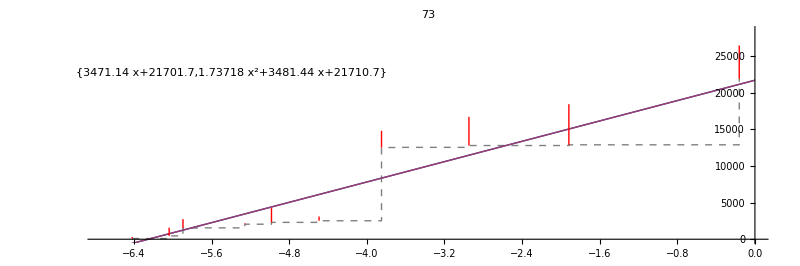

```mathematica
plotDonations@73
```

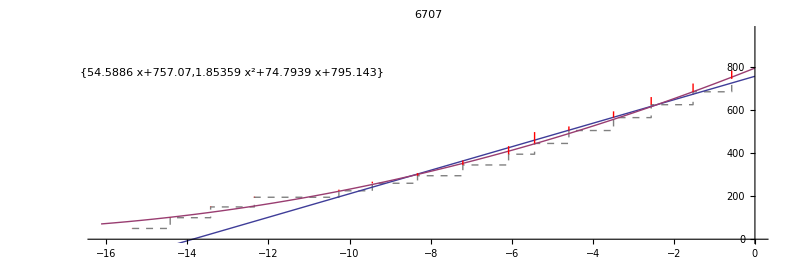

```mathematica
plotDonations@6707
```

```mathematica
points=contribs@73
```

{{-6.4192,90.,0.0380097},{-6.0384,450.,0.197838},{-5.8959,1530.,0.213469},{-5.7151,1550.,0.},{-5.2575,2050.,0.0175891},{-4.9836,2300.,0.343875},{-4.5178,2340.,0.},{-4.4932,2520.,0.102428},{-3.8493,12520.,0.400672},{-3.6877,12540.,0.},{-2.9479,12790.,0.688332},{-1.9178,12890.,0.974027},{-0.1616,21890.,0.799999}}

```mathematica
w=If[Length[points⟦1⟧]==3,Sqrt[points⟦All,3⟧],Table[1,{Length[points]}]]
```

{0.194961,0.444789,0.462027,0.,0.132624,0.586409,0.,0.320043,0.632987,0.,0.829658,0.986928,0.894427}

```mathematica
n=Length[points]
```

13

```mathematica
x1=points⟦All,1⟧*w
```

{-1.25149,-2.68582,-2.72406,0.,-0.69727,-2.92243,0.,-1.43802,-2.43656,0.,-2.44575,-1.89273,-0.144539}

```mathematica
x2=(points⟦All,1⟧)^2*w
```

{8.03357,16.218,16.0608,0.,3.6659,14.5642,0.,6.4613,9.37903,0.,7.20982,3.62988,0.0233576}

```mathematica
y=points⟦All,2⟧*w
```

{17.5465,200.155,706.901,0.,271.879,1348.74,0.,806.509,7924.99,0.,10611.3,12721.5,19579.}

```mathematica
x1t=Total[x1]
```

-18.6387

```mathematica
x2t=Total[x2]
```

85.2459

```mathematica
yt=Total[y]
```

54188.6

```mathematica
x1x1t=Total[x1*x1]
```

42.8168

```mathematica
x1x2t=Total[x1*x2]
```

-199.133

```mathematica
x2x2t=Total[x2*x2]
```

1005.94

```mathematica
x1yt=Total[x1*y]
```

-79946.8

```mathematica
x2yt=Total[x2*y]
```

238061.

```mathematica
x1m=x1t/n
```

-1.43374

```mathematica
x2m=x2t/n
```

6.55738

```mathematica
ym=yt/n
```

4168.35

```mathematica
sx1x1=x1x1t-x1t^2/n
```

16.0938

```mathematica
sx1x2=x1x2t-(x1t*x2t)/n
```

-76.9126

```mathematica
sx2x2=x2x2t-x2t^2/n
```

446.95

```mathematica
sx1y=x1yt-(yt*x1t)/n
```

-2254.3

```mathematica
sx2y=x2yt-(yt*x2t)/n
```

-117274.

```mathematica
b2=(sx1y*sx2x2-sx2y*sx1x2)/(sx2x2*sx1x1-sx1x2^2)
```

-7848.82

```mathematica
b3=(sx2y*sx1x1-sx1y*sx1x2)/(sx2x2*sx1x1-sx1x2^2)
```

-1613.04

```mathematica
b1=ym-b2*x1m-b3*x2m
```

3492.45

### Nice examples

{110,4681,5999,6707,11207,13362,14054,27050,27155,35761,39036,49489,55358}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

Plot::plln: Limiting value ∞ in {x, xMin$3649, xMax$3649} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in {ListPlot[{}, Joined → True, InterpolationOrder → 0, PlotStyle → {GrayLevel[0.5`], Dashing[{Small, Small}]}], Plot[wfit$3649, {x, xMin$3649, xMax$3649}, PlotStyle → {Automatic, Thick}], GraphicsBox[RGBColor[1, 0, 0]], GraphicsBox[List[]], GraphicsBox[List[GrayLevel[0], InsetBox[FormBox[RowBox[List[.

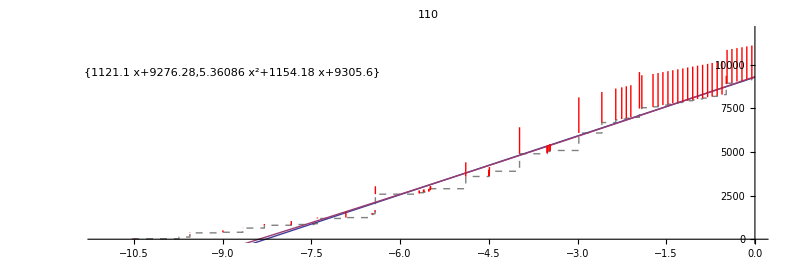
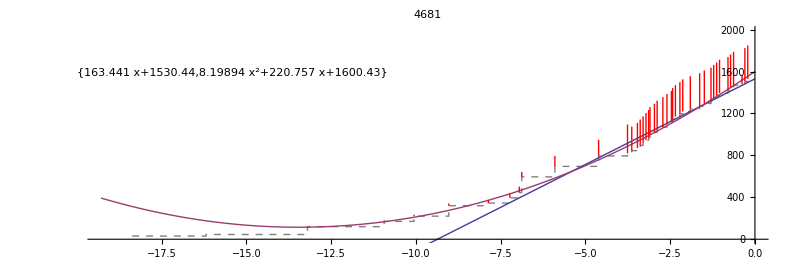
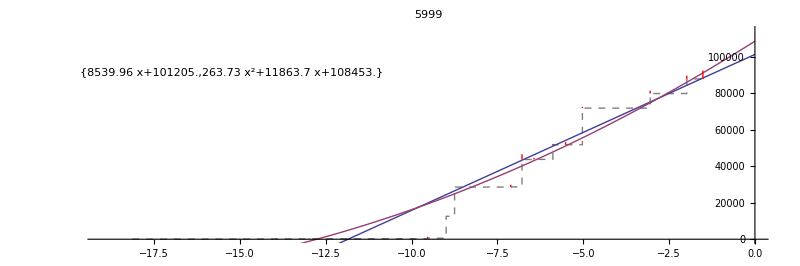
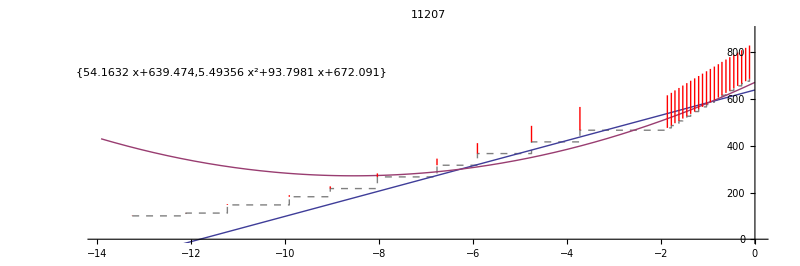
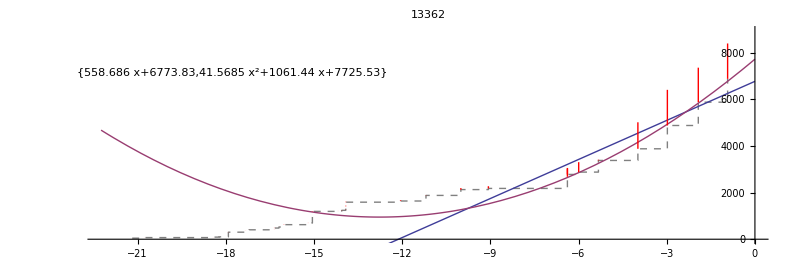
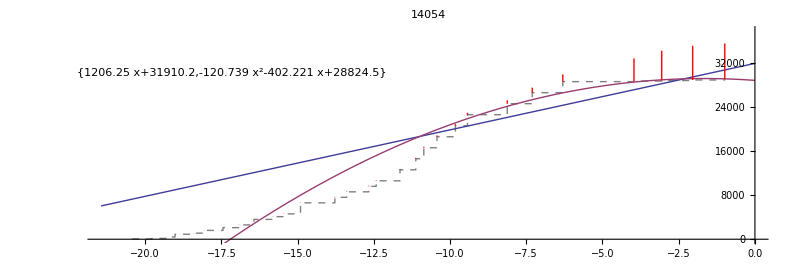
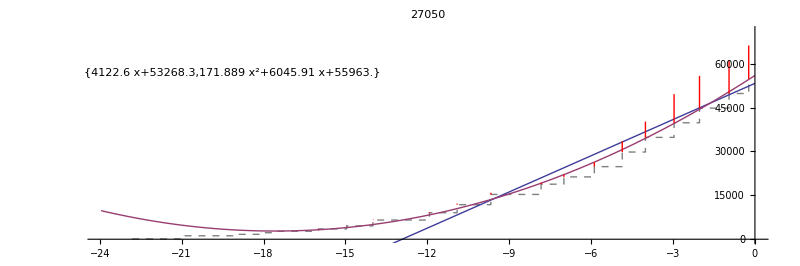
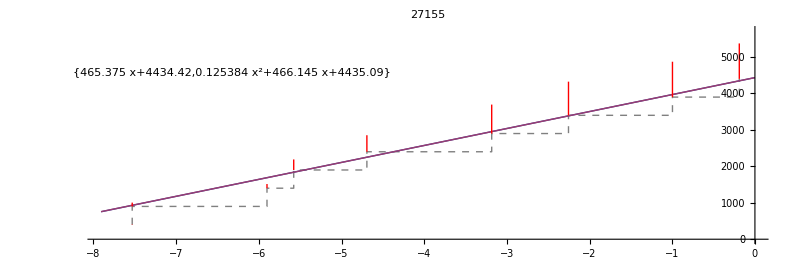
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
Show[{ListPlot[{},Joined→True,InterpolationOrder→0,PlotStyle→{GrayLevel[0.5],Dashing[{Small,Small}]}],Plot[wfit$3649,{x,xMin$3649,xMax$3649},PlotStyle→{Automatic,Thick}],-Graphics-,-Graphics-,-Graphics-},PlotRange→{{∞,0},{0,-∞}},AspectRatio→1/3,ImageSize→800,AxesOrigin→{0,0},PlotLabel→49489]
-Graphics-

```mathematica
examples=Sort@{39036,49489,27050,110,5999,6707,13362,4681,11207,14054,27155,55358,35761}
plotDonations/@examples//TableForm
```

### Tough examples

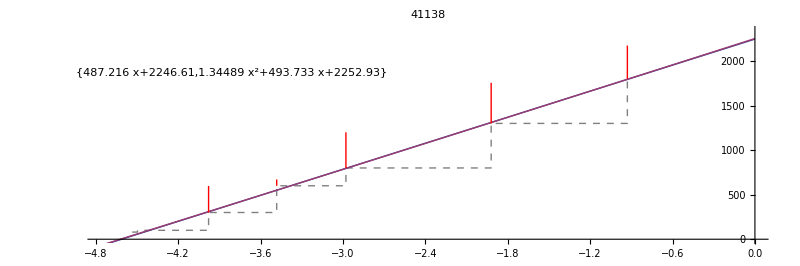

```mathematica
plotDonations@41138
```

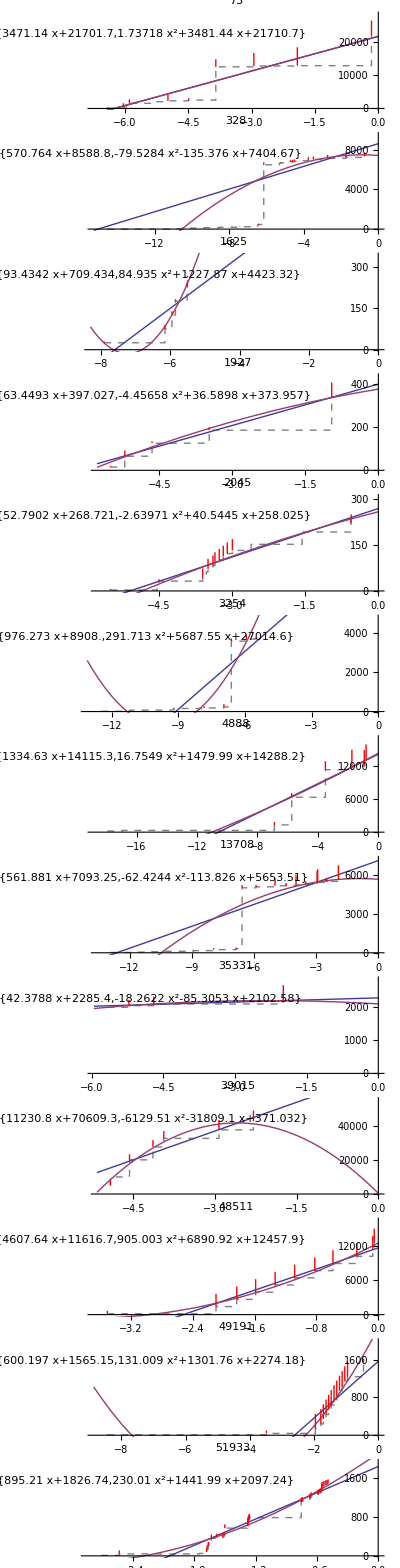

```mathematica
examples2=Sort@{49191,48511,39015,73,4888,328,1625,3254,2045,1927,13708,35331,51933};
plotDonations/@examples2//TableForm
```

### Testing

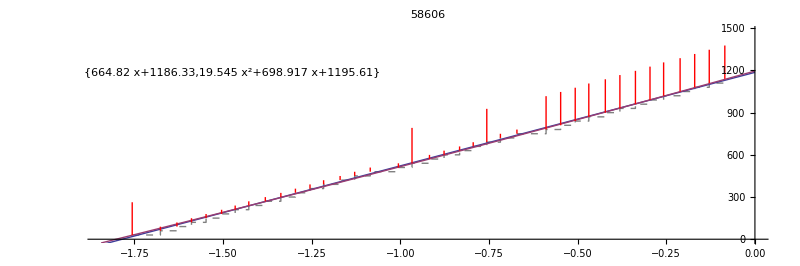

```mathematica
plotDonations/@{58606}//TableForm
```

### Quadratic tempering function

The rate

```mathematica
qtFunc:=qt:>Piecewise[{{fqtdlim-fqtdlim/(1+(-i/fqtddel)^fqtdshp), i<0}, {i/((1+(i/fqtalim)^4)^(1/4)), i≥0}}];
Manipulate[
Plot[qt,{i,-6,6},PlotRange->{-1.5,3},AspectRatio->1/3,ImageSize->600],
{{fqtalim,2,"ascension limit"},1,3},
{{fqtdlim,-1,"descension limit"},-1,-0.5},
{{fqtddel,3.5,"descension delay"},1,10},
{{fqtdshp,3.8,"descension sharpness"},2,8}]/.qtFunc
```

## Recency subtraction

```mathematica
subFunc:=sub:>fsubmax/(1+(ybn/fsubext)^fsubshp);
Manipulate[
Plot[sub,{ybn,0,1},
PlotRange->{0,fsubmax},
AspectRatio->1/2,
ImageSize->600,
GridLines->Automatic,
Ticks->{{#/12,ToString@#~~"m"}&/@Range[12],Automatic},
PlotLabel->"Recency subtraction"
],
{{fsubmax,1,"subtraction maximum"},1,2},
{{fsubext,0.5,"subtraction extent"},0.1,1},
{{fsubshp,5.8,"descension sharpness"},2,13}]/.subFunc
```

## Stretch function

ask amount is stretched by a factor of 1.2

## Rounding function

## Qualitative description

The rounding function takes a raw ask amount value and converts it to a round ask amount value. For example, if, based on all the complex math, we form a raw ask amount value of $247.11, then we’ll ask for a round $250. Similaryly, a raw value of $513.02 might get converted to $500. The raw value might go up or down, depending on where the nearest round value is.

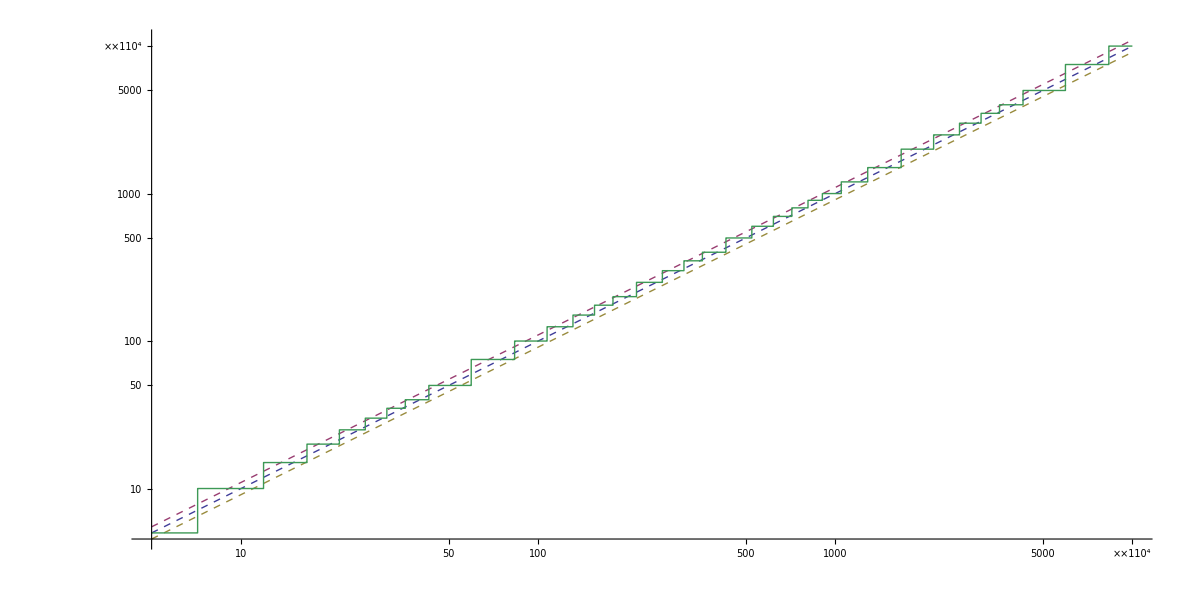

```mathematica
roundValues ={5,10,15,20,25,30,35,40,50,75,100,125,150,175,200,250,300,350,400,500,600,700,800,900,1000,1200,1500,2000,2500,3000,3500,4000,5000,7500,10000};
makeRound=Function[val,First@SortBy[roundValues,Abs[val*1.05-#]&]];
LogLogPlot[{x,1.1x,x/1.1,makeRound[x]},{x,5,10000},PlotPoints->500,ImageSize->1200,AspectRatio->1/2,GridLines->{roundValues,roundValues},PlotStyle->{{Dashed},{Dashed},{Dashed},{Thick}}]
```

# Likelihood algorithm

## Qualitative description

The likelihood is a number between 0 and 1, where 0 means very unlikely to give and 1 means very likely to give. It is based on the contributions, specifically the timing of the sequence of contributions as well as the contribution type of each one. 

At the outer-most level of the algorithm, the likelihood is the product of two factors called: dedication, and readiness.

Dedication: (valued between 0 and 1) If a bundle has been giving frequently and recently, it will have high dedication. Let us consider the affect of a single contribution on the dedication... Immediately after the contribution, the dedication will be high. But as time passes, the dedication will decay slowly and approach zero as time goes to infinity. The dedication decay function is responsible for this behavior. But what if a second contribution is received? At the point in time immediately before the second contribution comes, the dedication value (as decayed from the first contribution) is noted. Then, using this pre-contribution dedication value, a post-contribution dedication value is calulated using the dedication bolster function. Thus, the dedication has distinct values before the contribution and after, but at the instant the contribution is made, the dedication is undefined. Immediately after the contribution, the dedication will have risen, and then, from its new position, it will begin a new decay process.

This sequence of decay-bolster-decay-bolster continues sequentially across all contributions for the particular bundle until the current dedication value is found (using the point in time when the search is run), as decayed from the last contribution. Thus, calculating the dedication is an iterative process that must be performed in sequence across all contributions. When a bundle does not have any contributions, the dedication value is a function of the time since the first log entry (with the highest dedication being immediately after the first log entry, and decaying afterwards). 

Readiness: (valued between 0 and 1) After a donor gives, they’re not likely to give again for some time. This logic is the basis for the second likelihood factor, the readiness. Important contributions will force the readiness down to zero for a breif period of time. In turn, this forces the likelihood down to zero (due to multiplication), even though the dedication will be high immediately after the contribution. The readiness will rise to 1 much more quickly than the dedication will decay to zero, though. The readiness for a bundle is the product of all the specific readiness values (which also range from 0 to 1), as determined by each contribution. The specifc readiness function determines the specific readiness from one contribution.

## Constants (fixed values)

These values of these constants are fixed for the duraton of the search. The values are chosen through theoretical speculation, based on interacting with the Manipulate graphs below to produce sensible results. 

fdi	initial dedication value
frt	reliability decay time, in years
fdsr	dedication decay sharpness when fully reliable
fdsu	dedication decay sharpness when fully unreliable
fdwr	dedication decay weight when fully reliable
fdwu	dedication decay weight when fully unreliable
fbvz	bolster value at zero -- when optimism (co) is 1 and pre-contribution dedication (cdb) is 0 
fbsz	bolster slope at zero -- slope of cda vs cdb when co=1 and cdb=0
fbso	bolster slope at one -- slope of cda vs cdb when co=1 and cdb=1
frdcs	delayed readiness curve start
frdce	delayed readiness curve end

## Variables

These variable names will be used consistently in functions throughout the rest of this text. Due to the iterative nature of calculating the likelihood, some variables are specific to a context within the sequence of contributions for a given bundle. 

at an arbitrary point in time
ta	years between now and the date of the most recently prior affirmative event
tc	years between now and the date of the most recently prior contribution
rb	reliability 

for the current contribution
cybn	years before now
cop	optimism of the current contribution
crs	resilience of the current contribution
cta	years between the time of the current contribution and the most recently prior affirmative event
ctc	years between the time of the current contribution and the most recently prior contribution
cti	years between the time of the current contribution and the first (initial) log entry
crb	reliability at the time of the current contribution
cdbr	dedication immediately before the current contribution, if rb=1
cdbu	dedication immediately before the current contribution, if rb=0
cdb	dedication immediately before the current contribution
cda	dedication immediately after the current contribution 
cbs	bolster strength of the current contribution and its point in time
crdi	immediate readiness of the current contribution
crdd	readiness delay of the current contribution
crds	specific readiness of the current contribution

for the previous contribution
pop	optimism of the previous contribution
prs	resilience of the previous contribution
pta	years between the time of the previous contribution and the most recently prior affirmative event
ptc	years between the time of the previous contribution and the most recently prior contribution
prb	reliability at the time of the previous contribution
pda	dedication immediately after the previous contribution

## Functions

## Initial dedication value (cdb for the first contrib)

```mathematica
firstCdbFunc:=firstCdb:>fdbfmax/(1+(cti/fdbfdec)^fdbfshp);
Manipulate[Plot[firstCdb,{cti,0,5},PlotRange->{0,1}],
{{fdbfdec,3},0,4},
{{fdbfshp,2.2},1,4},
{{fdbfmax,0.3},0,1} ]/.firstCdbFunc
```

## Dedication decay function (to produce cdb for subsequent contribs)

Note that this function is contructed to be evaluated from the perspective of the contribution after the one that catylizes this dedication decay. Thus, the function does not require any input variables from the “current” contribution -- it just produces output of the variable db (dedication immediately before the current contribution). And this function does require input from the variables of the “previous” contribution (the contribution actually responsible for producing the decay curve).

### Reliability decay

```mathematica
rbFunc:=rb:>If[ta>frt,0,1-ta/frt];
prbFunc:=rbFunc/.{rb->prb,ta->pta};
```

```mathematica
Manipulate[Plot[#,{ta,0,5},AxesLabel->{"ta","rb"}],
{{frt,3,"decay time in years, frt"},2,4},SaveDefinitions->True]&@rb/.rbFunc
```

### Dedication decay function, with manipulated contants

```mathematica
cdbrFunc:=cdbr:>pda/(1+(fdwr ctc)^fdsr);
cdbuFunc:=cdbu:>pda/(1+(fdwu ctc)^fdsu);
cdbFunc:=cdb:>cdbu+(cdbr-cdbu)prb;
```

```mathematica
Manipulate[Plot[#,{ctc,0,7},PlotRange->{0,1},PlotStyle->{Automatic,Dashed,Dashed}],
{{prb,0.5,"reliability of previous contrib, prb"},0,1},
{{fdwr,0.22,"weight when reliable, fdwr"},0.01,1},
{{fdsr,3.7,"sharpness when reliable, fdsr"},1,8},
{{fdwu,0.5,"weight when UNreliable, fdwu"},0.01,1},
{{fdsu,1.8,"sharpness when UNreliable, fdsu"},1,8},
{{pda,1,"dedication after the previous contrib, pda"},0,1},
SaveDefinitions->True]&@{
cdb/.cdbFunc/.cdbrFunc/.cdbuFunc,
cdbr/.cdbrFunc,
cdbu/.cdbuFunc }
```

### Dedication decay function, in various forms

```mathematica
cdbFunc
```

cdb:>cdbu+(cdbr-cdbu) prb

```mathematica
cdbFunc/.cdbrFunc/.cdbuFunc
```

cdb:>pda/(1+(fdwu ctc)^fdsu)+(pda/(1+(fdwr ctc)^fdsr)-pda/(1+(fdwu ctc)^fdsu)) prb

```mathematica
Expand[(cdb/.cdbFunc/.cdbrFunc/.cdbuFunc)/pda]*pda
```

pda (1/(1+(ctc fdwu)^fdsu)+prb/(1+(ctc fdwr)^fdsr)-prb/(1+(ctc fdwu)^fdsu))

```mathematica
cdbFunc/.cdbrFunc/.cdbuFunc/.prbFunc
```

cdb:>pda/(1+(fdwu ctc)^fdsu)+(pda/(1+(fdwr ctc)^fdsr)-pda/(1+(fdwu ctc)^fdsu)) If[pta>frt,0,1-pta/frt]

## Dedication bolster function (to produce the cda value

### Bolster strength function

Resilient contributions maintain their strength even long after the last affirmative event. Contributions with zero resilience, will have only about 1/2 the

```mathematica
cbsFunc:=cbs:>cop/(1+(1-crs)^4 cta^2);
```

```mathematica
Manipulate[Plot[#,{cta,0,7},PlotRange->{0,1}],
{{crs,0,"resiliance of current contrib, crs"},0,1},
{{cop,1,"optimism of current contrib, cop"},0,1},
SaveDefinitions->True]&@cbs/.cbsFunc
```

### Dedication bolster function form

```mathematica
f[x_]:=a x^3+b x^2 +c x+d;
```

```mathematica
optimisticBolster=f[cdb]/.Solve[f[0]==fbvz&&f[1]==1&&f'[0]==fbsz&&f'[1]==fbso,{a,b,c,d}][[1]]
```

cdb fbsz+cdb^2 (3-fbso-2 fbsz-3 fbvz)+fbvz+cdb^3 (-2+fbso+fbsz+2 fbvz)

### Dedication bolster function, with manipulated contants

```mathematica
cdaFunc:=cda->cdb+(optimisticBolster-cdb)cbs;
```

```mathematica
Manipulate[Plot[#,{cdb,0,1},PlotRange->{0,1},Frame->True,PlotStyle->{Automatic,Dashed,Dashed}],
{{fbvz,0.47,"value at zero, fbvz"},0,1},
{{fbsz,0.15,"slope at zero, fbsz"},0,5},
{{fbso,0.15,"slope at one, fbso"},0,5},
{{cop,0.5,"optimism of this contrib, cop"},0,1},
{{crs,0,"resiliance of current contrib, crs"},0,1},
{{cta,0,"years between this contrib & last affirmative, cta"},0,7},
SaveDefinitions->True]&@{
cda/.cdaFunc/.cbsFunc,
optimisticBolster,
cdb}
```

### Dedication bolster function, in various forms

```mathematica
cdaFunc//FullSimplify
```

cda→cdb+cbs (fbvz+cdb ((-1+cdb) (1-fbsz+cdb (-2+fbso+fbsz))+cdb (-3+2 cdb) fbvz))

```mathematica
cda/.cdaFunc//Expand
```

cdb-cbs cdb+3 cbs cdb^2-2 cbs cdb^3-cbs cdb^2 fbso+cbs cdb^3 fbso+cbs cdb fbsz-2 cbs cdb^2 fbsz+cbs cdb^3 fbsz+cbs fbvz-3 cbs cdb^2 fbvz+2 cbs cdb^3 fbvz

```mathematica
Variables[cda/.cdaFunc]
```

{cdb,cbs,fbsz,fbso,fbvz}

```mathematica
cdaFunc/.cbsFunc//Simplify
```

cda→cdb+((-1+cdb) cop (-fbvz-cdb (-1+fbsz+fbvz)+cdb^2 (-2+fbso+fbsz+2 fbvz)))/(1+(-1+crs)^4 cta^2)

```mathematica
Variables[cda/.cdaFunc/.cdbFunc/.cdbrFunc/.cdbuFunc/.cbsFunc]
```

{cop,crs,cta,fbso,fbsz,fbvz,(ctc fdwr)^fdsr,(ctc fdwu)^fdsu,pda,prb}

## Readiness function (to produce the crds value)

```mathematica
f=c0+c1#+c2#^2+c3#^3+c4#^4+c5#^5&;
sol=Solve[f[0]==0&&f'[0]==0&&f''[0]==0&&f[1]==1&&f'[1]==0&&f''[1]==0,{c0,c1,c2,c3,c4,c5}];
f2=f/.sol[[1]];
f3=(1-startY)*f2[1/(endX-startX)(#-startX)]+startY&;
f4=If[#<startX,startY,If[#>endX,1,f3[#]]]&;
f4=Piecewise[{{startY,#<startX},{1,#>endX}},f3[#]]&;
Manipulate[Plot[#,{x,0,1},PlotRange->{0,1}],
{{startX,0.2},0,1},
{{startY,0.1},0,1},
{{endX,0.8},0,1},
SaveDefinitions->True]&@f4[x]
```

```mathematica
crds=f4[#]/.{startY->crdi,startX->crdd*frdcs,endX->crdd*frdce}&;
Manipulate[Plot[#,{ybn,0,1},PlotRange->{0,1},GridLines->{Range[0,1,1/12],{0,1/2,1}},
Ticks->{{#/12,ToString@#~~"m"}&/@Range[12],Automatic}],
{{frdcs,0.1,"curve start (frdcs)"},0,1},
{{frdce,1,"curve end (frdce)"},0,1},
{{crdi,0,"initial"},0,1},
{{crdd,1,"delay"},0,1},
SaveDefinitions->True]&@crds[ybn]
```

```mathematica
crds[ybn]//Simplify
```

Piecewise[{{crdi, ybn<crdd frdcs}, {1, ybn>crdd frdce}, {crdi+((-1+crdi) (crdd frdcs-ybn)^3 (crdd^2 (10 frdce^2-5 frdce frdcs+frdcs^2)+3 crdd (-5 frdce+frdcs) ybn+6 ybn^2))/(crdd^5 (frdce-frdcs)^5), True}}]

# Priority algorithm

## Functions

```mathematica
priorityFunc:=priority:>likelihood(1-1/(1+(fprasc*aaRaw)^fprshp));
Manipulate[
LogLinearPlot[priority,{aaRaw,0.1,10000},PlotRange->{0,1}],
{{fprasc,0.03},0.001,0.05},
{{fprshp,0.9},0.5,2},
{{likelihood,1},0,1}
]/.priorityFunc
```

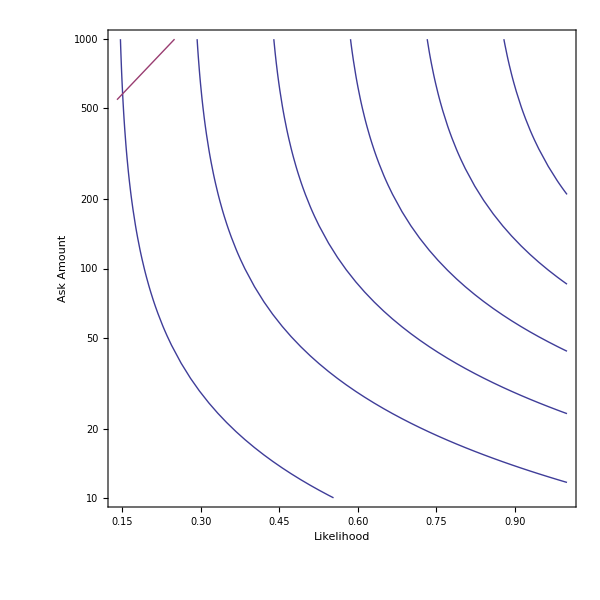

```mathematica
eqn=(priority/.priorityFunc/.{fprasc->3/100,fprshp->9/10}/.{aaRaw->a,likelihood->k})==p;
exp=a/.Solve[eqn,a][[1]];
LogPlot[
{Table[exp,{p,0.14,1,0.14}],
Table[10^(2.4(k+d)),{d,Range[9]}]
},
{k,0.14,1},PlotRange->{10,1000},
Frame->True,FrameLabel->{"Likelihood","Ask Amount"},
ImageSize->600,AspectRatio->1]
```

```mathematica
Table[10^(2(k+d)),{d,{}}]
```

{}

## Analysis

## Behavior for bundles without contributions

Only relevant for direct mail, so all constants are DM values

```mathematica
baselineFunc
firstCdbFunc
priorityFunc
```

baseline:>fblmax/(1+(yafl/fbldec)^fblshp)

firstCdb:>fdbfmax/(1+(cti/fdbfdec)^fdbfshp)

priority:>likelihood (1-1/(1+(fprasc aaRaw)^fprshp))

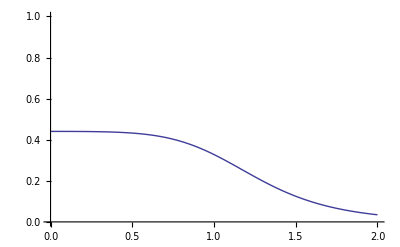

```mathematica
constants={
askStretch->1.2,
(* baseline ask amount constants *)
fbldec->2,
fblshp->2.5,
fblmax->50,
(* dedication *)
fdbfdec->1.3,
fdbfshp->5,
fdbfmax->0.7,
(* priority contstants *)
fprasc->0.03,
fprshp->0.9
};
noContribPriority=priority/.priorityFunc/.{aaRaw->baseline*askStretch,likelihood->firstCdb}/.baselineFunc/.firstCdbFunc/.{cti->yafl}/.constants;
Plot[noContribPriority,{yafl,0,2},PlotRange->{0,1}]
```

# Difficulty algorithm

```mathematica
eqn=(priority/.priorityFunc/.{fprasc->3/100,fprshp->9/10}/.{aaRaw->a,likelihood->k})==p;
exp=a/.Solve[eqn,a][[1]];
Manipulate[LogPlot[
{Table[exp,{p,0.14,1,0.14}],
Table[E^(fdiffslope(k+fdiffspacing*d+fdiffoffset)),{d,Range[9]}]
},
{k,0.14,1},PlotRange->{10,1000},
Frame->True,FrameLabel->{"Likelihood","Ask Amount"},
ImageSize->600,AspectRatio->1],
{{fdiffslope,6},5,7},
{{fdiffspacing,0.12},0.1,0.2},
{{fdiffoffset,-0.4},-0.7,-0.3}]
```

```mathematica
E^(fdiffslope(k+fdiffspacing*d+fdiffoffset))/.{fdiffslope->6,fdiffspacing->12/100,fdiffoffset->-4/10}
```

ⅇ^(6 (-2/5+(3 d)/25+k))

```mathematica
Solve[E^(fdiffslope(k+fdiffspacing*d+fdiffoffset))==a,d,Reals]
```

{{d→ConditionalExpression[(-fdiffoffset fdiffslope-fdiffslope k+Log[a])/(fdiffslope fdiffspacing),a>0]}}

```mathematica
dificultyFunc=d:>(-fdiffoffset fdiffslope-fdiffslope k+Log[a])/(fdiffslope fdiffspacing)
```

d:>(-fdiffoffset fdiffslope-fdiffslope k+Log[a])/(fdiffslope fdiffspacing)

# Analysis of results

#### Database

```mathematica
Needs["DatabaseLink`"]
civi=OpenSQLConnection["local_bnb1civi"];
```

#### Ask amount values

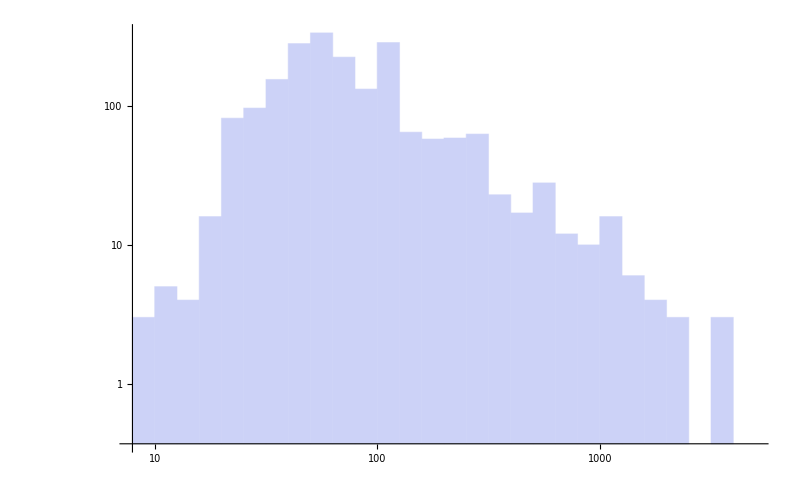

```mathematica
aaval=Flatten@SQLExecute[civi,"select aa_raw from bundle where is_chosen = 1;"];
Histogram[aaval,"Log","LogCount",ImageSize->800]
```

#### Likelihood values

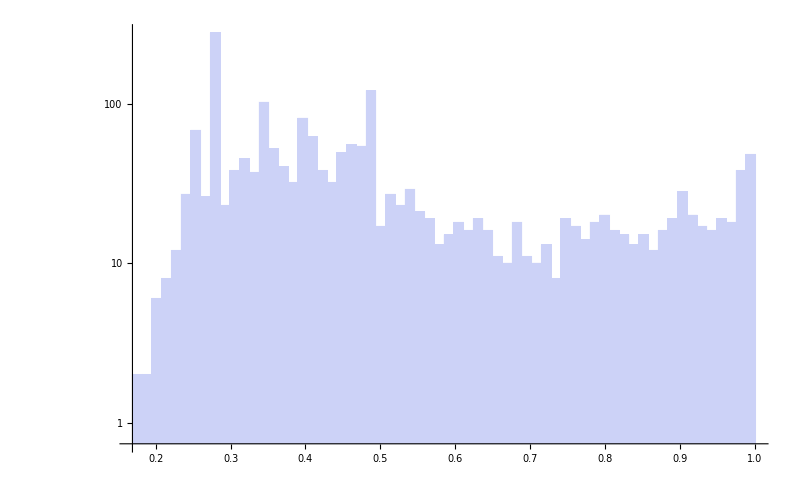

```mathematica
lhval=Flatten@SQLExecute[civi,"select likelihood from bundle where is_chosen = 1;" ];
Histogram[lhval,{0.013},{"Log","Count"},ImageSize->800]
```

#### Ask amount / Likelihood 2D histogram

```mathematica
data=SQLExecute[civi,"select likelihood, aa_raw from bundle where is_chosen = 1;"];
```

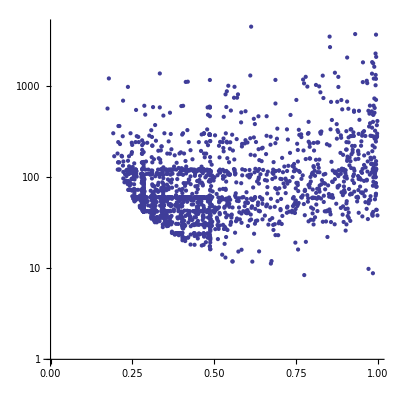

```mathematica
ListLogPlot[data,PlotRange->All,AxesOrigin->{0,0},AspectRatio->1]
```

#### Ask amount / Likelihood 2D histogram with priority and difficulty

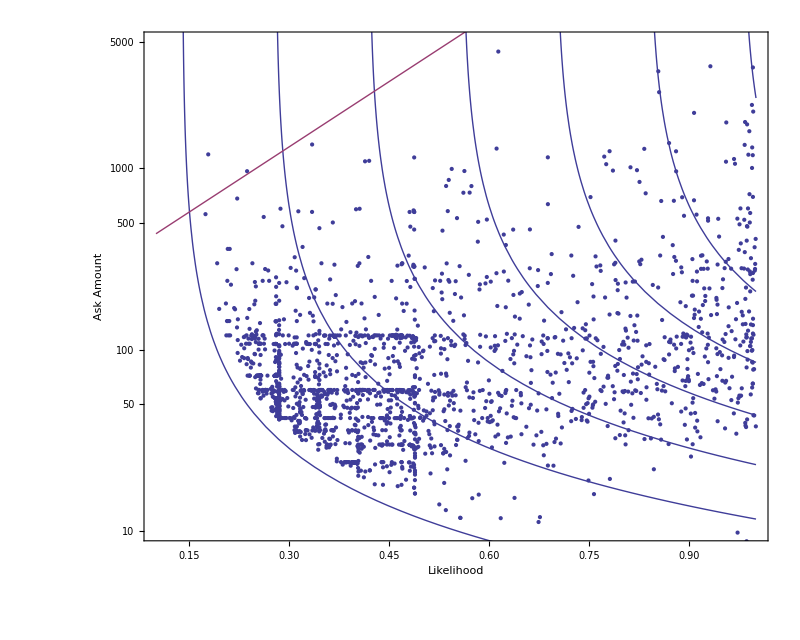

```mathematica
Show[
ListLogPlot[data,PlotRange->{{0.1,1},{10,5000}},AxesOrigin->{0,8}],

LogPlot[
{Table[exp,{p,0.1395,1,0.14}],
Table[10^(2.4(k+d)),{d,Range[9]}]
},
{k,0.1,1}],

Frame->True,ImageSize->800,AspectRatio->0.8,FrameLabel->{"Likelihood","Ask Amount"}]
```

#### Ask amount / Likelihood 2D histogram with priority, proportionally divided

```mathematica
priorityValues=Flatten@SQLExecute[civi,"select priority from bundle where is_chosen=1;"];
```

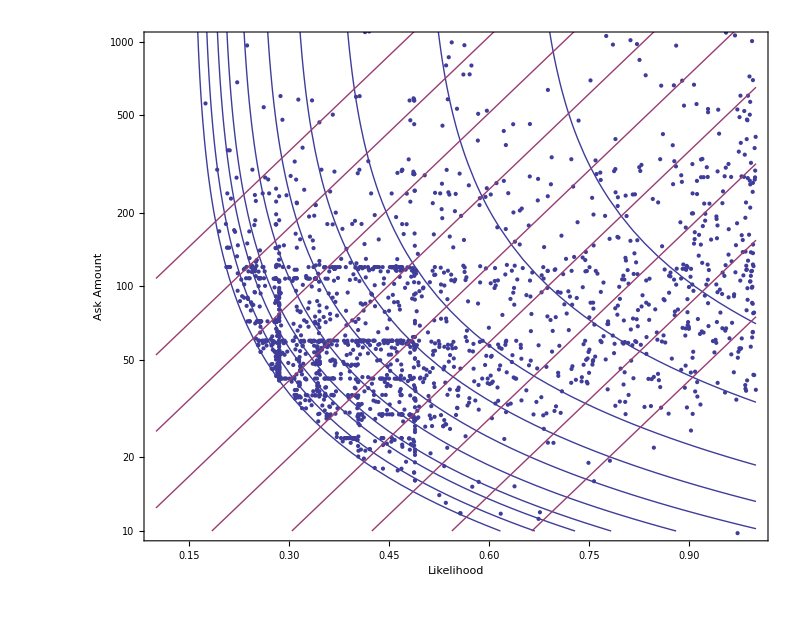

```mathematica
priorityDivisions=Min@@@Partition[Sort[priorityValues],Floor[Length[priorityValues]/10]];
Show[
ListLogPlot[data,PlotRange->{{0.1,1},{10,1000}},AxesOrigin->{0,8}],

LogPlot[
{Table[exp,{p,priorityDivisions}],
Table[ⅇ^(6 (-2/5+(3 d)/25+k)),{d,Range[9]}]
},
{k,0.1,1},PlotRange->{10,5000}],

Frame->True,ImageSize->800,AspectRatio->0.8,FrameLabel->{"Likelihood","Ask Amount"}]
```

```mathematica
priorityDivisions
```

{0.155898,0.168949,0.1842,0.197895,0.22254,0.256552,0.303014,0.371556,0.501924,0.662012}

# Scrap